((-1+pp)^2 (1+pp))/pp

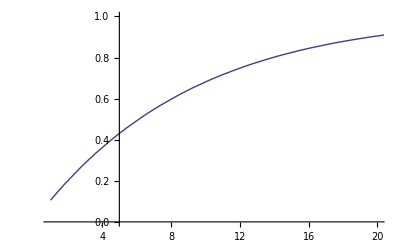

```mathematica
Simplify[∑_(t=2)^∞ (t*pp*(1-pp)^t)]

Pn[α_,n_]:=1-(1-α/180)^n

ExpectedTime[α_]:=(Pn[α]+1)*(Pn[α]-1)^2/Pn[α]

Plot[Pn[x,20],{x,1,180},PlotRange-> {{1,180},{0,1}}]
```